# Verification of NAO Center of Mass

## Import Logs

### Center of Mass

```mathematica
FileAddress="D:/log_wb_zero.txt";
Data = Import[FileAddress,"Data"];


Xsensor:=Data[[All,25]];
Ysensor:=Data[[All,26]];
Zsensor:=Data[[All,27]];

Xcommand:=Data[[All,28]];
Ycommand:=Data[[All,29]];
Zcommand:=Data[[All,30]];
```

### Head Angles

```mathematica
Subscript[θHD, 1]:=Data[[All,1]];
Subscript[θHD, 2]:=Data[[All,2]];

Subscript[θLH, 1]:=Data[[All,3]];
Subscript[θLH, 2]:=Data[[All,4]];
Subscript[θLH, 3]:=Data[[All,5]];
Subscript[θLH, 4]:=Data[[All,6]];
Subscript[θLH, 5]:=Data[[All,7]];

Subscript[θRH, 1]:=Data[[All,8]];
Subscript[θRH, 2]:=Data[[All,9]];
Subscript[θRH, 3]:=Data[[All,10]];
Subscript[θRH, 4]:=Data[[All,11]];
Subscript[θRH, 5]:=Data[[All,12]];

Subscript[θLL, 1]:=Data[[All,13]];
Subscript[θLL, 2]:=Data[[All,14]];
Subscript[θLL, 3]:=Data[[All,15]];
Subscript[θLL, 4]:=Data[[All,16]];
Subscript[θLL, 5]:=Data[[All,17]];
Subscript[θLL, 6]:=Data[[All,18]];

Subscript[θRL, 1]:=Data[[All,19]];
Subscript[θRL, 2]:=Data[[All,20]];
Subscript[θRL, 3]:=Data[[All,21]];
Subscript[θRL, 4]:=Data[[All,22]];
Subscript[θRL, 5]:=Data[[All,23]];
Subscript[θRL, 6]:=Data[[All,24]];
```

## Head

```mathematica
DHPHead:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θHD, 1]}, {0, 0, 0, Subscript[θHD, 2]}});

(*Subscript[θHD, 1]:=0;
Subscript[θHD, 2]:=0;*)

aah := DHPHead[[2;;-1,1]];
bh := DHPHead[[2;;-1,2]];
αh := DHPHead[[2;;-1,3]];
θh:= DHPHead[[2;;-1,4]];


qh[i_, j_]:=({{Cos[θh[[i, j]]], -Cos[αh [[i]]]Sin[θh[[i, j]]], Sin[αh [[i]]]Sin[θh[[i, j]]]}, {Sin[θh[[i, j]]], Cos[αh [[i]]]Cos[θh[[i, j]]], -Sin[αh [[i]]]Cos[θh[[i, j]]]}, {0, Sin[αh[[i]]], Cos[αh[[i]]]}});

ah[i_, j_]:=({{aah[[i]]Cos[θh[[i, j]]]}, {aah[[i]]Sin[θh[[i, j]]]}, {bh[[i]]}});

QHD3to1[j_]:=qh[1,j].qh[2,j];
PHD3to1[j_]:=ah[1,j]+qh[1,j].ah[2,j];
THD3to1[j_]:=({{QHD3to1[j][[1,1]], QHD3to1[j][[1,2]], QHD3to1[j][[1,3]], PHD3to1[j][[1,1]]}, {QHD3to1[j][[2,1]], QHD3to1[j][[2,2]], QHD3to1[j][[2,3]], PHD3to1[j][[2,1]]}, {QHD3to1[j][[3,1]], QHD3to1[j][[3,2]], QHD3to1[j][[3,3]], PHD3to1[j][[3,1]]}, {0, 0, 0, 1}});
```

```mathematica
THD1toTorso:=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, -1, 0, 0.1265}, {0, 0, 0, 1}});
THD3toTorso[j_]:=THD1toTorso.THD3to1[j];

THD3to1[1]//MatrixForm
THD3toTorso[1]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.1265
0. | 0. | 0. | 1.)

```mathematica
THD3toTorso[1]//MatrixForm
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.1265
0. | 0. | 0. | 1.)

```mathematica
THD3toTorso[1]//MatrixForm
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.1265
0. | 0. | 0. | 1.)

## hhh

```mathematica
THD3toTorso[1]//MatrixForm
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.1265
0. | 0. | 0. | 1.)

## Lef Hand

```mathematica
DHPLH:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θLH, 1]}, {Subscript[lh, 1], 0, π/2, Subscript[θLH, 2]+π/2}, {0, Subscript[lh, 2], π/2, Subscript[θLH, 3]+π}, {0, 0, π/2, Subscript[θLH, 4]+π}, {0, Subscript[lh, 3], 0, Subscript[θLH, 5]}})

Subscript[lh, 1]=0.015;
Subscript[lh, 2]=0.105;
Subscript[lh, 3]=0.05595;

aalh := DHPLH[[2;;-1,1]];
blh := DHPLH[[2;;-1,2]];
αlh := DHPLH[[2;;-1,3]];
θlh := DHPLH[[2;;-1,4]];

qLH[i_, j_]:=({{Cos[θlh[[i, j]]], -Cos[αlh [[i]]]Sin[θlh[[i, j]]], Sin[αlh [[i]]]Sin[θlh[[i, j]]]}, {Sin[θlh[[i, j]]], Cos[αlh [[i]]]Cos[θlh[[i, j]]], -Sin[αlh [[i]]]Cos[θlh[[i, j]]]}, {0, Sin[αlh[[i]]], Cos[αlh[[i]]]}});

aLH[i_, j_]:=({{aalh[[i]]Cos[θlh[[i, j]]]}, {aalh[[i]]Sin[θlh[[i, j]]]}, {blh[[i]]}});

QLH6to1[j_]:=qLH[1,j].qLH[2,j].qLH[3,j].qLH[4,j].qLH[5,j];
PLH6to1[j_]:=aLH[1,j]+qLH[1,j].aLH[2,j]+qLH[1,j].qLH[2,j].aLH[3,j]+qLH[1,j].qLH[2,j].qLH[3,j].aLH[4,j]+qLH[1,j].qLH[2,j].qLH[3,j].qLH[4,j].aLH[5,j];
TLH6to1[j_]:=({{QLH6to1[j][[1,1]], QLH6to1[j][[1,2]], QLH6to1[j][[1,3]], PLH6to1[j][[1,1]]}, {QLH6to1[j][[2,1]], QLH6to1[j][[2,2]], QLH6to1[j][[2,3]], PLH6to1[j][[2,1]]}, {QLH6to1[j][[3,1]], QLH6to1[j][[3,2]], QLH6to1[j][[3,3]], PLH6to1[j][[3,1]]}, {0, 0, 0, 1}});
TLH1toTorso= ({{1, 0, 0, 0}, {0, 0, 1, 0.098}, {0, -1, 0, 0.100}, {0, 0, 0, 1}});
TLH6to1[1]//MatrixForm
TLH6toTorso[j_]:=TLH1toTorso.TLH6to1[j];

QLH2to1[j_]:=qLH[1,j];
PLH2to1[j_]:=aLH[1,j];
TLH2to1[j_]:=({{QLH2to1[j][[1,1]], QLH2to1[j][[1,2]], QLH2to1[j][[1,3]], PLH2to1[j][[1,1]]}, {QLH2to1[j][[2,1]], QLH2to1[j][[2,2]], QLH2to1[j][[2,3]], PLH2to1[j][[2,1]]}, {QLH2to1[j][[3,1]], QLH2to1[j][[3,2]], QLH2to1[j][[3,3]], PLH2to1[j][[3,1]]}, {0, 0, 0, 1}});
QLH3to1[j_]:=qLH[1,j].qLH[2,j];
PLH3to1[j_]:=aLH[1,j]+qLH[1,j].aLH[2,j];
TLH3to1[j_]:=({{QLH3to1[j][[1,1]], QLH3to1[j][[1,2]], QLH3to1[j][[1,3]], PLH3to1[j][[1,1]]}, {QLH3to1[j][[2,1]], QLH3to1[j][[2,2]], QLH3to1[j][[2,3]], PLH3to1[j][[2,1]]}, {QLH3to1[j][[3,1]], QLH3to1[j][[3,2]], QLH3to1[j][[3,3]], PLH3to1[j][[3,1]]}, {0, 0, 0, 1}});
QLH4to1[j_]:=qLH[1,j].qLH[2,j].qLH[3,j];
PLH4to1[j_]:=aLH[1,j]+qLH[1,j].aLH[2,j]+qLH[1,j].qLH[2,j].aLH[3,j];
TLH4to1[j_]:=({{QLH4to1[j][[1,1]], QLH4to1[j][[1,2]], QLH4to1[j][[1,3]], PLH4to1[j][[1,1]]}, {QLH4to1[j][[2,1]], QLH4to1[j][[2,2]], QLH4to1[j][[2,3]], PLH4to1[j][[2,1]]}, {QLH4to1[j][[3,1]], QLH4to1[j][[3,2]], QLH4to1[j][[3,3]], PLH4to1[j][[3,1]]}, {0, 0, 0, 1}});

QLH5to1[j_]:=qLH[1,j].qLH[2,j].qLH[3,j].qLH[4,j];
PLH5to1[j_]:=aLH[1,j]+qLH[1,j].aLH[2,j]+qLH[1,j].qLH[2,j].aLH[3,j]+qLH[1,j].qLH[2,j].qLH[3,j].aLH[4,j];
TLH5to1[j_]:=({{QLH5to1[j][[1,1]], QLH5to1[j][[1,2]], QLH5to1[j][[1,3]], PLH5to1[j][[1,1]]}, {QLH5to1[j][[2,1]], QLH5to1[j][[2,2]], QLH5to1[j][[2,3]], PLH5to1[j][[2,1]]}, {QLH5to1[j][[3,1]], QLH5to1[j][[3,2]], QLH5to1[j][[3,3]], PLH5to1[j][[3,1]]}, {0, 0, 0, 1}});
TLH5toTorso[j_]:=TLH1toTorso.TLH5to1[j];
TLH5toTorso[1]//MatrixForm
```

(0 | 0 | 1 | 0.16095
0 | -1 | 0 | 0.
1 | 0 | 0 | 0.015
0 | 0 | 0 | 1)

(0. | 0. | 1. | 0.105
1. | 0. | 0. | 0.113
0. | 1. | 0. | 0.1
0. | 0. | 0. | 1.)

## Right Hand

```mathematica
DHPRH:=({{"a", "b", "α", "θ"}, {0, 0, π/2, Subscript[θRH, 1]}, {Subscript[lh, 1], 0, -π/2, Subscript[θRH, 2]-π/2}, {0, Subscript[lh, 2], π/2, Subscript[θRH, 3]}, {0, 0, π/2, Subscript[θRH, 4]+π}, {0, Subscript[lh, 3], 0, Subscript[θRH, 5]}})

Subscript[lh, 1]=0.015;
Subscript[lh, 2]=0.105;
Subscript[lh, 3]=0.05595;

aarh := DHPRH[[2;;-1,1]];
brh := DHPRH[[2;;-1,2]];
αrh := DHPRH[[2;;-1,3]];
θrh:= DHPRH[[2;;-1,4]];

qRH[i_, j_]:=({{Cos[θrh[[i, j]]], -Cos[αrh [[i]]]Sin[θrh[[i, j]]], Sin[αrh [[i]]]Sin[θrh[[i, j]]]}, {Sin[θrh[[i, j]]], Cos[αrh [[i]]]Cos[θrh[[i, j]]], -Sin[αrh [[i]]]Cos[θrh[[i, j]]]}, {0, Sin[αrh[[i]]], Cos[αrh[[i]]]}});

aRH[i_, j_]:=({{aarh[[i]]Cos[θrh[[i, j]]]}, {aarh[[i]]Sin[θrh[[i, j]]]}, {brh[[i]]}});

QRH6to1[j_]:=qRH[1,j].qRH[2,j].qRH[3,j].qRH[4,j].qRH[5,j];
PRH6to1[j_]:=aRH[1,j]+qRH[1,j].aRH[2,j]+qRH[1,j].qRH[2,j].aRH[3,j]+qRH[1,j].qRH[2,j].qRH[3,j].aRH[4,j]+qRH[1,j].qRH[2,j].qRH[3,j].qRH[4,j].aRH[5,j];
TRH6to1[j_]:=({{QRH6to1[j][[1,1]], QRH6to1[j][[1,2]], QRH6to1[j][[1,3]], PRH6to1[j][[1,1]]}, {QRH6to1[j][[2,1]], QRH6to1[j][[2,2]], QRH6to1[j][[2,3]], PRH6to1[j][[2,1]]}, {QRH6to1[j][[3,1]], QRH6to1[j][[3,2]], QRH6to1[j][[3,3]], PRH6to1[j][[3,1]]}, {0, 0, 0, 1}});
TRH1toTorso= ({{1, 0, 0, 0}, {0, 0, 1, -0.098}, {0, -1, 0, 0.100}, {0, 0, 0, 1}});
TRH6toTorso[j_]:=TRH1toTorso.TRH6to1[j];

QRH2to1[j_]:=qRH[1,j];
PRH2to1[j_]:=aRH[1,j];
TRH2to1[j_]:=({{QRH2to1[j][[1,1]], QRH2to1[j][[1,2]], QRH2to1[j][[1,3]], PRH2to1[j][[1,1]]}, {QRH2to1[j][[2,1]], QRH2to1[j][[2,2]], QRH2to1[j][[2,3]], PRH2to1[j][[2,1]]}, {QRH2to1[j][[3,1]], QRH2to1[j][[3,2]], QRH2to1[j][[3,3]], PRH2to1[j][[3,1]]}, {0, 0, 0, 1}});
QRH3to1[j_]:=qRH[1,j].qRH[2,j];
PRH3to1[j_]:=aRH[1,j]+qRH[1,j].aRH[2,j];
TRH3to1[j_]:=({{QRH3to1[j][[1,1]], QRH3to1[j][[1,2]], QRH3to1[j][[1,3]], PRH3to1[j][[1,1]]}, {QRH3to1[j][[2,1]], QRH3to1[j][[2,2]], QRH3to1[j][[2,3]], PRH3to1[j][[2,1]]}, {QRH3to1[j][[3,1]], QRH3to1[j][[3,2]], QRH3to1[j][[3,3]], PRH3to1[j][[3,1]]}, {0, 0, 0, 1}});
QRH4to1[j_]:=qRH[1,j].qRH[2,j].qRH[3,j];
PRH4to1[j_]:=aRH[1,j]+qRH[1,j].aRH[2,j]+qRH[1,j].qRH[2,j].aRH[3,j];
TRH4to1[j_]:=({{QRH4to1[j][[1,1]], QRH4to1[j][[1,2]], QRH4to1[j][[1,3]], PRH4to1[j][[1,1]]}, {QRH4to1[j][[2,1]], QRH4to1[j][[2,2]], QRH4to1[j][[2,3]], PRH4to1[j][[2,1]]}, {QRH4to1[j][[3,1]], QRH4to1[j][[3,2]], QRH4to1[j][[3,3]], PRH4to1[j][[3,1]]}, {0, 0, 0, 1}});

QRH5to1[j_]:=qRH[1,j].qRH[2,j].qRH[3,j].qRH[4,j];
PRH5to1[j_]:=aRH[1,j]+qRH[1,j].aRH[2,j]+qRH[1,j].qRH[2,j].aRH[3,j]+qRH[1,j].qRH[2,j].qRH[3,j].aRH[4,j];
TRH5to1[j_]:=({{QRH5to1[j][[1,1]], QRH5to1[j][[1,2]], QRH5to1[j][[1,3]], PRH5to1[j][[1,1]]}, {QRH5to1[j][[2,1]], QRH5to1[j][[2,2]], QRH5to1[j][[2,3]], PRH5to1[j][[2,1]]}, {QRH5to1[j][[3,1]], QRH5to1[j][[3,2]], QRH5to1[j][[3,3]], PRH5to1[j][[3,1]]}, {0, 0, 0, 1}});
TRH5toTorso[j_]:=TRH1toTorso.TRH5to1[j];
TRH5toTorso[1]//MatrixForm
```

(0. | 0. | 1. | 0.105
1. | 0. | 0. | -0.113
0. | 1. | 0. | 0.1
0. | 0. | 0. | 1.)

## Left Leg

```mathematica
DHPLL:=({{"a", "b", "α", "θ"}, {0, 0, π/4, Subscript[θLL, 1]}, {0, 0, π/2, Subscript[θLL, 2]+π/2}, {Subscript[ll, 1], 0, π/2, Subscript[θLL, 3]+π}, {Subscript[ll, 2], 0, 0, Subscript[θLL, 4]}, {0, 0, π/2, Subscript[θLL, 5]+π}, {Subscript[ll, 3], 0, 0, Subscript[θLL, 6]+π}})

Subscript[ll, 1]=0.100;
Subscript[ll, 2]=0.1029;
Subscript[ll, 3]=0.04519;

aall := DHPLL[[2;;-1,1]];
bll := DHPLL[[2;;-1,2]];
αll := DHPLL[[2;;-1,3]];
θll := DHPLL[[2;;-1,4]];

qLL[i_, j_]:=({{Cos[θll[[i, j]]], -Cos[αll [[i]]]Sin[θll[[i, j]]], Sin[αll [[i]]]Sin[θll[[i, j]]]}, {Sin[θll[[i, j]]], Cos[αll [[i]]]Cos[θll[[i, j]]], -Sin[αll [[i]]]Cos[θll[[i, j]]]}, {0, Sin[αll[[i]]], Cos[αll[[i]]]}});

aLL[i_, j_]:=({{aall[[i]]Cos[θll[[i, j]]]}, {aall[[i]]Sin[θll[[i, j]]]}, {bll[[i]]}});

QLL7to1[j_]:=qLL[1,j].qLL[2,j].qLL[3,j].qLL[4,j].qLL[5,j].qLL[6,j];
PLL7to1[j_]:=aLL[1,j]+qLL[1,j].aLL[2,j]+qLL[1,j].qLL[2,j].aLL[3,j]+qLL[1,j].qLL[2,j].qLL[3,j].aLL[4,j]+qLL[1,j].qLL[2,j].qLL[3,j].qLL[4,j].aLL[5,j]+qLL[1,j].qLL[2,j].qLL[3,j].qLL[4,j].qLL[5,j].aLL[6,j];
TLL7to1[j_]:=({{QLL7to1[j][[1,1]], QLL7to1[j][[1,2]], QLL7to1[j][[1,3]], PLL7to1[j][[1,1]]}, {QLL7to1[j][[2,1]], QLL7to1[j][[2,2]], QLL7to1[j][[2,3]], PLL7to1[j][[2,1]]}, {QLL7to1[j][[3,1]], QLL7to1[j][[3,2]], QLL7to1[j][[3,3]], PLL7to1[j][[3,1]]}, {0, 0, 0, 1}});
TLL1toTorso=({{1, 0, 0, 0}, {0, (√2)/2, -(√2)/2, 0.050}, {0, (√2)/2, (√2)/2, -0.085}, {0, 0, 0, 1}});
TLL7toTorso[j_]:=TLL1toTorso.TLL7to1[j];

QLL6to1[j_]:=qLL[1,j].qLL[2,j].qLL[3,j].qLL[4,j].qLL[5,j];
PLL6to1[j_]:=aLL[1,j]+qLL[1,j].aLL[2,j]+qLL[1,j].qLL[2,j].aLL[3,j]+qLL[1,j].qLL[2,j].qLL[3,j].aLL[4,j]+qLL[1,j].qLL[2,j].qLL[3,j].qLL[4,j].aLL[5,j];
TLL6to1[j_]:=({{QLL6to1[j][[1,1]], QLL6to1[j][[1,2]], QLL6to1[j][[1,3]], PLL6to1[j][[1,1]]}, {QLL6to1[j][[2,1]], QLL6to1[j][[2,2]], QLL6to1[j][[2,3]], PLL6to1[j][[2,1]]}, {QLL6to1[j][[3,1]], QLL6to1[j][[3,2]], QLL6to1[j][[3,3]], PLL6to1[j][[3,1]]}, {0, 0, 0, 1}});
TLL6toTorso[j_]:=TLL1toTorso.TLL6to1[j];
QLL2to1[j_]:=qLL[1,j];
PLL2to1[j_]:=aLL[1,j];
TLL2to1[j_]:=({{QLL2to1[j][[1,1]], QLL2to1[j][[1,2]], QLL2to1[j][[1,3]], PLL2to1[j][[1,1]]}, {QLL2to1[j][[2,1]], QLL2to1[j][[2,2]], QLL2to1[j][[2,3]], PLL2to1[j][[2,1]]}, {QLL2to1[j][[3,1]], QLL2to1[j][[3,2]], QLL2to1[j][[3,3]], PLL2to1[j][[3,1]]}, {0, 0, 0, 1}});
QLL3to1[j_]:=qLL[1,j].qLL[2,j];
PLL3to1[j_]:=aLL[1,j]+qLL[1,j].aLL[2,j];
TLL3to1[j_]:=({{QLL3to1[j][[1,1]], QLL3to1[j][[1,2]], QLL3to1[j][[1,3]], PLL3to1[j][[1,1]]}, {QLL3to1[j][[2,1]], QLL3to1[j][[2,2]], QLL3to1[j][[2,3]], PLL3to1[j][[2,1]]}, {QLL3to1[j][[3,1]], QLL3to1[j][[3,2]], QLL3to1[j][[3,3]], PLL3to1[j][[3,1]]}, {0, 0, 0, 1}});
QLL4to1[j_]:=qLL[1,j].qLL[2,j].qLL[3,j];
PLL4to1[j_]:=aLL[1,j]+qLL[1,j].aLL[2,j]+qLL[1,j].qLL[2,j].aLL[3,j];
TLL4to1[j_]:=({{QLL4to1[j][[1,1]], QLL4to1[j][[1,2]], QLL4to1[j][[1,3]], PLL4to1[j][[1,1]]}, {QLL4to1[j][[2,1]], QLL4to1[j][[2,2]], QLL4to1[j][[2,3]], PLL4to1[j][[2,1]]}, {QLL4to1[j][[3,1]], QLL4to1[j][[3,2]], QLL4to1[j][[3,3]], PLL4to1[j][[3,1]]}, {0, 0, 0, 1}});
TLL4toTorso[j_]:=TLL1toTorso.TLL4to1[j];
PLL4to2in2[j_]:=aLL[2,j]+qLL[2,j].aLL[3,j];

QLL5to1[j_]:=qLL[1,j].qLL[2,j].qLL[3,j].qLL[4,j];
PLL5to1[j_]:=aLL[1,j]+qLL[1,j].aLL[2,j]+qLL[1,j].qLL[2,j].aLL[3,j]+qLL[1,j].qLL[2,j].qLL[3,j].aLL[4,j];
TLL5to1[j_]:=({{QLL5to1[j][[1,1]], QLL5to1[j][[1,2]], QLL5to1[j][[1,3]], PLL5to1[j][[1,1]]}, {QLL5to1[j][[2,1]], QLL5to1[j][[2,2]], QLL5to1[j][[2,3]], PLL5to1[j][[2,1]]}, {QLL5to1[j][[3,1]], QLL5to1[j][[3,2]], QLL5to1[j][[3,3]], PLL5to1[j][[3,1]]}, {0, 0, 0, 1}});
PLL5to2in2[j_]:=aLL[2,j]+qLL[2,j].aLL[3,j]+qLL[2,j].qLL[3,j].aLL[4,j];
PLL5to2in2[1]//MatrixForm
```

(0.
-0.2029
0.)

## Right Leg

```mathematica
DHPRL:=({{"a", "b", "α", "θ"}, {0, 0, π/4, Subscript[θRL, 1]}, {0, 0, π/2, Subscript[θRL, 2]-π/2}, {Subscript[ll, 1], 0, -π/2, Subscript[θRL, 3]}, {Subscript[ll, 2], 0, 0, Subscript[θRL, 4]}, {0, 0, π/2, Subscript[θRL, 5]}, {Subscript[ll, 3], 0, 0, Subscript[θRL, 6]}})
Subscript[ll, 1]=0.100;
Subscript[ll, 2]=0.1029;
Subscript[ll, 3]=0.04519;


aarl := DHPRL[[2;;-1,1]];
brl := DHPRL[[2;;-1,2]];
αrl := DHPRL[[2;;-1,3]];
θrl := DHPRL[[2;;-1,4]];


qRL[i_, j_]:=({{Cos[θrl[[i, j]]], -Cos[αrl [[i]]]Sin[θrl[[i, j]]], Sin[αrl [[i]]]Sin[θrl[[i, j]]]}, {Sin[θrl[[i, j]]], Cos[αrl [[i]]]Cos[θrl[[i, j]]], -Sin[αrl [[i]]]Cos[θrl[[i, j]]]}, {0, Sin[αrl[[i]]], Cos[αrl[[i]]]}});

aRL[i_, j_]:=({{aarl[[i]]Cos[θrl[[i, j]]]}, {aarl[[i]]Sin[θrl[[i, j]]]}, {brl[[i]]}});

QRL7to1[j_]:=qRL[1,j].qRL[2,j].qRL[3,j].qRL[4,j].qRL[5,j].qRL[6,j];
PRL7to1[j_]:=aRL[1,j]+qRL[1,j].aRL[2,j]+qRL[1,j].qRL[2,j].aRL[3,j]+qRL[1,j].qRL[2,j].qRL[3,j].aRL[4,j]+qRL[1,j].qRL[2,j].qRL[3,j].qRL[4,j].aRL[5,j]+qRL[1,j].qRL[2,j].qRL[3,j].qRL[4,j].qRL[5,j].aRL[6,j];
TRL7to1[j_]:=({{QRL7to1[j][[1,1]], QRL7to1[j][[1,2]], QRL7to1[j][[1,3]], PRL7to1[j][[1,1]]}, {QRL7to1[j][[2,1]], QRL7to1[j][[2,2]], QRL7to1[j][[2,3]], PRL7to1[j][[2,1]]}, {QRL7to1[j][[3,1]], QRL7to1[j][[3,2]], QRL7to1[j][[3,3]], PRL7to1[j][[3,1]]}, {0, 0, 0, 1}});
TRL1toTorso:=({{-1, 0, 0, 0}, {0, -(√2)/2, (√2)/2, -0.050}, {0, (√2)/2, (√2)/2, -0.085}, {0, 0, 0, 1}});
TRL7toTorso[j_]:=TRL1toTorso.TRL7to1[j];


QRL6to1[j_]:=qRL[1,j].qRL[2,j].qRL[3,j].qRL[4,j].qRL[5,j];
PRL6to1[j_]:=aRL[1,j]+qRL[1,j].aRL[2,j]+qRL[1,j].qRL[2,j].aRL[3,j]+qRL[1,j].qRL[2,j].qRL[3,j].aRL[4,j]+qRL[1,j].qRL[2,j].qRL[3,j].qRL[4,j].aRL[5,j];
TRL6to1[j_]:=({{QRL6to1[j][[1,1]], QRL6to1[j][[1,2]], QRL6to1[j][[1,3]], PRL6to1[j][[1,1]]}, {QRL6to1[j][[2,1]], QRL6to1[j][[2,2]], QRL6to1[j][[2,3]], PRL6to1[j][[2,1]]}, {QRL6to1[j][[3,1]], QRL6to1[j][[3,2]], QRL6to1[j][[3,3]], PRL6to1[j][[3,1]]}, {0, 0, 0, 1}});
TRL6toTorso[j_]:=TRL1toTorso.TRL6to1[j];
QRL2to1[j_]:=qRL[1,j];
PRL2to1[j_]:=aRL[1,j];
TRL2to1[j_]:=({{QRL2to1[j][[1,1]], QRL2to1[j][[1,2]], QRL2to1[j][[1,3]], PRL2to1[j][[1,1]]}, {QRL2to1[j][[2,1]], QRL2to1[j][[2,2]], QRL2to1[j][[2,3]], PRL2to1[j][[2,1]]}, {QRL2to1[j][[3,1]], QRL2to1[j][[3,2]], QRL2to1[j][[3,3]], PRL2to1[j][[3,1]]}, {0, 0, 0, 1}});
QRL3to1[j_]:=qRL[1,j].qRL[2,j];
PRL3to1[j_]:=aRL[1,j]+qRL[1,j].aRL[2,j];
TRL3to1[j_]:=({{QRL3to1[j][[1,1]], QRL3to1[j][[1,2]], QRL3to1[j][[1,3]], PRL3to1[j][[1,1]]}, {QRL3to1[j][[2,1]], QRL3to1[j][[2,2]], QRL3to1[j][[2,3]], PRL3to1[j][[2,1]]}, {QRL3to1[j][[3,1]], QRL3to1[j][[3,2]], QRL3to1[j][[3,3]], PRL3to1[j][[3,1]]}, {0, 0, 0, 1}});
QRL4to1[j_]:=qRL[1,j].qRL[2,j].qRL[3,j];
PRL4to1[j_]:=aRL[1,j]+qRL[1,j].aRL[2,j]+qRL[1,j].qRL[2,j].aRL[3,j];
TRL4to1[j_]:=({{QRL4to1[j][[1,1]], QRL4to1[j][[1,2]], QRL4to1[j][[1,3]], PRL4to1[j][[1,1]]}, {QRL4to1[j][[2,1]], QRL4to1[j][[2,2]], QRL4to1[j][[2,3]], PRL4to1[j][[2,1]]}, {QRL4to1[j][[3,1]], QRL4to1[j][[3,2]], QRL4to1[j][[3,3]], PRL4to1[j][[3,1]]}, {0, 0, 0, 1}});
TRL4toTorso[j_]:=TRL1toTorso.TRL4to1[j];
PRL4to2in2[j_]:=aRL[2,j]+qRL[2,j].aRL[3,j];

QRL5to1[j_]:=qRL[1,j].qRL[2,j].qRL[3,j].qRL[4,j];
PRL5to1[j_]:=aRL[1,j]+qRL[1,j].aRL[2,j]+qRL[1,j].qRL[2,j].aRL[3,j]+qRL[1,j].qRL[2,j].qRL[3,j].aRL[4,j];
TRL5to1[j_]:=({{QRL5to1[j][[1,1]], QRL5to1[j][[1,2]], QRL5to1[j][[1,3]], PRL5to1[j][[1,1]]}, {QRL5to1[j][[2,1]], QRL5to1[j][[2,2]], QRL5to1[j][[2,3]], PRL5to1[j][[2,1]]}, {QRL5to1[j][[3,1]], QRL5to1[j][[3,2]], QRL5to1[j][[3,3]], PRL5to1[j][[3,1]]}, {0, 0, 0, 1}});
PRL5to2in2[j_]:=aRL[2,j]+qRL[2,j].aRL[3,j]+qRL[2,j].qRL[3,j].aRL[4,j];
PRL5to2in2[1]//MatrixForm
```

(0.
-0.2029
0.)

## Center of Mass

### Torso

```mathematica
(*Torso*)
mTorso=1.0496;
comTorso=({{-0.00413}, {0}, {0.04342}, {1}});
PcomTorso=comTorso;

(*Neck:3*)
mNeck=0.06442;
comNeck=({{-0.00001}, {0}, {-0.02742}, {1}});
THD3toTorso[1]//MatrixForm
PcomNeck[j_]:=THD3toTorso[j].comNeck;
PcomNeck[1]//MatrixForm
THD3to1[1]//MatrixForm
(*Head:1*)
mHead=0.60533;
comHead=({{-0.00112}, {-0.05258}, {0}, {1}});
PcomHead[j_]:=THD1toTorso.({{Cos[Subscript[θHD, 1][[j]]], -Sin[Subscript[θHD, 1][[j]]], 0, 0}, {Sin[Subscript[θHD, 1][[j]]], Cos[Subscript[θHD, 1][[j]]], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).comHead;
PcomHead[1]//MatrixForm;
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.1265
0. | 0. | 0. | 1.)

(-0.00001
0.
0.09908
1.)

(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

### Hands

```mathematica
(*Arms*)

(*RightShoulderPitch*)
mShoulder=0.07504;
comRShoulder=({{-0.00165}, {-0.00014}, {0.02663}, {1}});
TRShoulderTRH1[j_]:=({{Cos[Subscript[θRH, 1][[j]]], Sin[Subscript[θRH, 1][[j]]], 0, 0}, {-Sin[Subscript[θRH, 1][[j]]], Cos[Subscript[θRH, 1][[j]]], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
PcomRShoulder[j_]:=TRH1toTorso.TRShoulderTRH1[j].comRShoulder;

(*LeftShoulderPitch*)
comLShoulder=({{-0.00165}, {-0.00014}, {-0.02663}, {1}});
TLShoulderTLH1[j_]:=({{Cos[Subscript[θLH, 1][[j]]], Sin[Subscript[θLH, 1][[j]]], 0, 0}, {-Sin[Subscript[θLH, 1][[j]]], Cos[Subscript[θLH, 1][[j]]], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
PcomLShoulder[j_]:=TLH1toTorso.TLShoulderTLH1[j].comLShoulder;



(*Biceps*)

(*Right*)
mBiceps:=0.15777;
comRBiceps:=({{0.02455}, {-0.00563}, {0.0033}, {1}});

PcomRBiceps[j_]:=TRH1toTorso.TRH2to1[j].comRBiceps;

(*Left*)
comLBiceps:=({{0.02455}, {0.00563}, {0.0033}, {1}});
PcomLBiceps[j_]:=TLH1toTorso.TLH2to1[j].comLBiceps;



(*Elbow*)

(*Right*)
mElbow:=0.06483;
comRElbow:=({{0}, {0.00014}, {Subscript[lh, 2]-0.02744}, {1}});

PcomRElbow[j_]:=TRH1toTorso.TRH3to1[j].comRElbow;

(*Left*)
comLElbow:=({{0}, {-0.00014}, {Subscript[lh, 2]-0.02744}, {1}});

PcomLElbow[j_]:=TLH1toTorso.TLH3to1[j].comLElbow;


(*FArm*)

(*Right*)
mFArm:=0.07761;
comRFArm:=({{0.00281}, {0.02556}, {0.00076}, {1}});
PcomRFArm[j_]:=TRH1toTorso.TRH4to1[j].comRFArm;

(*Left*)
comLFArm:=({{-0.00281}, {0.02556}, {0.00076}, {1}});
PcomLFArm[j_]:=TLH1toTorso.TLH4to1[j].comLFArm;



(*Hands*)

(*Right*)
mHands:=0.18533;
comRHand:=({{0.00088}, {0.00308}, {0.03434}, {1}});
PcomRHand[j_]:=TRH1toTorso.TRH6to1[j].comRHand;

(*Left*)
comLHand:=({{-0.00088}, {0.00308}, {0.03434}, {1}});
PcomLHand[j_]:=TLH1toTorso.TLH6to1[j].comLHand;
```

### Legs

```mathematica
(*Legs*)

(*Pelvis: HipYawPitch:1*)
mPelvis:=0.06981;

(*RightPelvis*)
comRPelvis:=({{-1, 0, 0, 0}, {0, -(√2)/2, (√2)/2, 0}, {0, (√2)/2, (√2)/2, 0}, {0, 0, 0, 1}}).({{-0.00781}, {0.01114}, {0.02661}, {1}});
TRLegTRL1[j_]:=({{Cos[Subscript[θRL, 1][[j]]], Sin[Subscript[θRL, 1][[j]]], 0, 0}, {-Sin[Subscript[θRL, 1][[j]]], Cos[Subscript[θRL, 1][[j]]], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
PcomRPelvis[j_]:=TRL1toTorso.TRLegTRL1[j].comRPelvis;

(*LeftPelvis*)
comLPelvis:=({{1, 0, 0, 0}, {0, (√2)/2, (√2)/2, 0}, {0, (-√2)/2, (√2)/2, 0}, {0, 0, 0, 1}}).({{-0.00781}, {-0.01114}, {0.02661}, {1}});
TLLegTLL1[j_]:=({{Cos[Subscript[θLL, 1][[j]]], Sin[Subscript[θLL, 1][[j]]], 0, 0}, {-Sin[Subscript[θLL, 1][[j]]], Cos[Subscript[θLL, 1][[j]]], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
PcomLPelvis[j_]:=TLL1toTorso.TLLegTLL1[j].comLPelvis;

(*Hip: HipRoll:3*)
mHip:=0.13053;

(*RightHip*)
comRHip:=({{0.00515}, {-0.00029}, {-0.01549}, {1}});

(*PcomRHand:=TRH1toTorso.TRH6to1.comRHand;*)
PcomRHip[j_]:=TRL1toTorso.TRL3to1[j].comRHip;

(*LeftHip*)

comLHip:=({{-0.00515}, {-0.00029}, {-0.01549}, {1}});
PcomLHip[j_]:=TLL1toTorso.TLL3to1[j].comLHip;

(*Thigh:HipPitch:2*)
mThigh:=0.38968;

(*RightThigh*)
comRThigh:=({{-0.00138}, {-0.05373}, {-0.00221}, {1}});
PcomRThigh[j_]:=TRL1toTorso.TRL2to1[j].comRThigh;
(*LeftThigh*)
comLThigh:=({{0.00138}, {-0.05373}, {-0.00221}, {1}});
PcomLThigh[j_]:=TLL1toTorso.TLL2to1[j].comLThigh;

(*Tibia:KneePitch:4*)
mTibia:=0.29142;

(*RightTibia*)
comRTibia:=({{0.04936}, {-0.00453}, {-0.00225}, {1}});
PcomRTibia[j_]:=TRL1toTorso.TRL4to1[j].comRTibia;

(*LeftTibia*)
comLTibia:=({{0.04936}, {0.00453}, {-0.00225}, {1}});
PcomLTibia[j_]:=TLL1toTorso.TLL4to1[j].comLTibia;

(*Ankle:AnklePitch:5*)
mAnkle:=0.13416;

(*RightAnkle*)
comRAnkle:=({{-0.00685}, {-0.00045}, {-0.00029}, {1}});
PcomRAnkle[j_]:=TRL1toTorso.TRL5to1[j].comRAnkle;
(*LeftAnkle*)
comLAnkle:=({{-0.00685}, {0.00045}, {-0.00029}, {1}});
PcomLAnkle[j_]:=TLL1toTorso.TLL5to1[j].comLAnkle;

(*Feet:AnkleRoll:6*)
mFoot:=0.16184;
(*RightFoot*)

comRFoot:=({{0.03239}, {-0.0033}, {0.02542}, {1}});
PcomRFoot[j_]:=TRL1toTorso.TRL6to1[j].comRFoot;
(*LeftFoot*)
comLFoot:=({{-0.03239}, {-0.0033}, {0.02542}, {1}});
PcomLFoot[j_]:=TLL1toTorso.TLL6to1[j].comLFoot;
```

### Computation of the Center of Mass

P_com=(∑_(i=1)^n m_i P_i)/(∑_(i=1)^n m_i)

```mathematica
Mtotal=mTorso+mNeck+mHead+2mShoulder+2mBiceps+2mElbow+2mFArm+2mHands+2mPelvis+2mHip+2mThigh+2mTibia+2mAnkle+2mFoot;

Ptotal[j_]:=mTorso*PcomTorso+mNeck*PcomNeck[j]+mHead*PcomHead[j]+mShoulder*PcomRShoulder[j]+mShoulder*PcomLShoulder[j]+mBiceps*PcomRBiceps[j]+mBiceps*PcomLBiceps[j]+mElbow*PcomRElbow[j]+mElbow*PcomLElbow[j]+mFArm*PcomRFArm[j]+mFArm*PcomLFArm[j]+mHands*PcomRHand[j]+mHands*PcomLHand[j]+mPelvis*PcomRPelvis[j]+mPelvis*PcomLPelvis[j]+mHip*PcomRHip[j]+mHip*PcomLHip[j]+mThigh*PcomRThigh[j]+mThigh*PcomLThigh[j]+mTibia*PcomRTibia[j]+mTibia*PcomLTibia[j]+mAnkle*PcomLAnkle[j]+mAnkle*PcomRAnkle[j]+mFoot*PcomRFoot[j]+mFoot*PcomLFoot[j];
```

```mathematica
comNAO[j_]:=Ptotal[j]*1/Mtotal;
```

```mathematica
i = 100
comNAO[i]//MatrixForm
({{Xsensor[[i]]}, {Ysensor[[i]]}, {Zsensor[[i]]}, {1}})//MatrixForm
```

100

(0.00660229
-0.00546986
-0.028353
1.)

(0.0039832
-0.00564867
-0.0277161
1)

```mathematica
({{Xcommand[[i]]}, {Ycommand[[i]]}, {Zcommand[[i]]}})//MatrixForm
```

(0.00408004
-0.00666883
-0.0271817)

```mathematica
Subscript[θLL, 2][[1]]
```

0

```mathematica
PcomTorso//MatrixForm
```

(-0.00413
0
0.04342
1)

```mathematica
PcomNeck[1]//MatrixForm
```

(-0.00001
0.
0.09908
1.)

```mathematica
PcomHead[1]//MatrixForm
```

(-0.00112
0.
0.17908
1.)

```mathematica
PcomRShoulder[1]//MatrixForm
```

(-0.00165
-0.07137
0.10014
1.)

```mathematica
PcomLShoulder[1]//MatrixForm
```

(-0.00165
0.07137
0.10014
1.)

```mathematica
PcomRBiceps[1]//MatrixForm
```

(0.02455
-0.10363
0.1033
1.)

```mathematica
PcomLBiceps[1]//MatrixForm
```

(0.02455
0.10363
0.1033
1.)

```mathematica
PcomRElbow[1]//MatrixForm
```

(0.07756
-0.113
0.09986
1.)

```mathematica
PcomLElbow[1]//MatrixForm
```

(0.07756
0.113
0.09986
1.)

```mathematica
PcomRFArm[1]//MatrixForm
```

(0.13056
-0.11581
0.10076
1.)

```mathematica
PcomLFArm[1]//MatrixForm
```

(0.13056
0.11581
0.10076
1.)

```mathematica
PcomRHand[1]//MatrixForm
```

(0.19529
-0.11212
0.10308
1.)

```mathematica
PcomLHand[1]//MatrixForm
```

(0.19529
0.11212
0.10308
1.)

```mathematica
PcomRPelvis[1]//MatrixForm
```

(-0.00781
-0.03886
-0.05839
1.)

```mathematica
PcomLPelvis[1]//MatrixForm
```

(-0.00781
0.03886
-0.05839
1.)

```mathematica
PcomRHip[1]//MatrixForm
```

(-0.01549
-0.05029
-0.09015
1.)

```mathematica
PcomLHip[1]//MatrixForm
```

(-0.01549
0.05029
-0.09015
1.)

```mathematica
PcomRThigh[1]//MatrixForm
```

(0.00138
-0.05221
-0.13873
1.)

```mathematica
PcomLThigh[1]//MatrixForm
```

(0.00138
0.05221
-0.13873
1.)

```mathematica
PcomRTibia[1]//MatrixForm
```

(0.00453
-0.05225
-0.23436
1.)

```mathematica
PcomLTibia[1]//MatrixForm
```

(0.00453
0.05225
-0.23436
1.)

```mathematica
PcomLAnkle[1]//MatrixForm
```

(0.00045
0.05029
-0.28105
1.)

```mathematica
PcomRAnkle[1]//MatrixForm
```

(0.00045
-0.05029
-0.28105
1.)

```mathematica
PcomRFoot[1]//MatrixForm
```

(0.02542
-0.0533
-0.32029
1.)

```mathematica
PcomLFoot[1]//MatrixForm
```

(0.02542
0.0533
-0.32029
1.)

## Plot

```mathematica
Xsensor//MatrixForm;
```

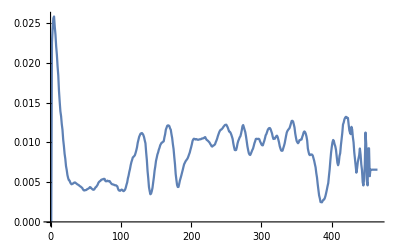

```mathematica
ListLinePlot[%572]
```

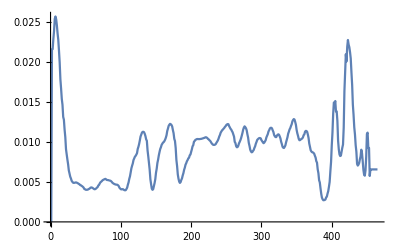

```mathematica
Xcommand;
```

```mathematica
ListLinePlot[%574]
```

-Graphics-

comNAO[1,1]